# Quadratic potential for Quantum Drude Oscillators

```mathematica
Print["Running automatic cells!"]
```

Running automatic cells!

## Quartic Schrodinger equation and triconfluent Heun function (ONGOING)

### Spectrum (reproduce Heuuuun Lay paper, symmetric case) (SUCCESS)

We define the potential and the Schrodinger equation

```mathematica
V[z_]:=A z +z^2+λ^2 z^4
eq[ψ_]:=z↦ ψ''[z]-V[z]ψ[z]+ϵ ψ[z];
```

We perfoms two change of the active variable ψ:
- the exponential of cubic polynomial brings us to a standard triconfluent form
- the (z+1)^(some power)allows to get nice polynomial coeffients in the ODE eventually, hence nice difference equations

```mathematica
eq2[w_]:=z↦1/(ⅇ^(-z/(2 λ)-(z^3 λ)/3)(z+1)^(-A/(2λ)-1))eq[z↦ⅇ^(-z/(2 λ)-(z^3 λ)/3)(z+1)^(-A/(2λ)-1)w[z]][z]//FullSimplify
```

```mathematica
Coefficient[eq2[w][z],w[z]]//FullSimplify
Coefficient[eq2[w][z],w'[z]]//FullSimplify
Coefficient[eq2[w][z],w''[z]]//FullSimplify
```

((1+A+z)^2+2 (2+3 A+2 z) λ+4 (2-A z (1+z)+(1+z)^2 ϵ) λ^2-8 z (1+z) λ^3)/(4 (1+z)^2 λ^2)

-(1+A+z+2 λ+2 z^2 (1+z) λ^2)/((1+z) λ)

1

We perform a change of passive variable to move to the [0,1] segment

```mathematica
Solve[{x==z/(z+1)},{z}]//FullSimplify
```

{{z→-x/(-1+x)}}

```mathematica
eq3[w_]:=x↦(eq2[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
```

```mathematica
CoefficientList[Coefficient[eq3[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{-(1+A+4 λ)/λ,12+(2+3 A)/λ,-(1+3 A+2 λ (6+λ))/λ,4+A/λ}

{(1+A^2+A (2+6 λ)+4 λ (1+(2+ϵ) λ))/(4 λ^2),-((A+2 λ) (1+A+2 λ (2+λ)))/(2 λ^2),((A+2 λ) (A+4 λ))/(4 λ^2)}

The coefficients of the ODE are simple polynomials now. Let us extract and name the coefficients of those polynomials

```mathematica
a=1;
b=-4;
c=6;
d=-4;
e=1;
f=-(1+A+4 λ)/λ;
g=12+(2+3 A)/λ;
h=-(1+3 A+2 λ (6+λ))/λ;
i=4+A/λ;
j=(1+A^2+A (2+6 λ)+4 λ (1+(2+ϵ) λ))/(4 λ^2);
k=-((A+2 λ) (1+A+2 λ (2+λ)))/(2 λ^2);l=((A+2 λ) (A+4 λ))/(4 λ^2);
```

Ansatz for w(x)=∑α_n x^n, we get the following difference equations

```mathematica
diffEq[n_]:=(n+1)(n+2)a Subscript[α, n+2]+(n(n+1)b+(n+1)f)Subscript[α, n+1]+((n-1)n c+n g+j)Subscript[α, n]+((n-2)(n-1)d+(n-1)h+k)Subscript[α, n-1]+((n-3)(n-2)e+(n-2)i+l)Subscript[α, n-2]
```

The initial condition C0, C1 are fixed according to the paper of Lay.
We also gather the two first equations

```mathematica
C0=1;
C1=1+1/(2λ);
initialEq={Subscript[α, 0]-C0,Subscript[α, 1]-C1,2a Subscript[α, 2]+f Subscript[α, 1]+j Subscript[α, 0],6a Subscript[α, 3]+2(b+f)Subscript[α, 2]+(g+j)Subscript[α, 1]+k Subscript[α, 0]};
```

We solve for the coefficients of the series expansion for a large value of n

```mathematica
Nmax=20;
αlarge=Solve[Thread[Join[initialEq,Table[diffEq[n],{n,2,Nmax-2}]]==0],Table[Subscript[α, m],{m,0,Nmax}]][[1,Nmax+1,2]];
```

The zeros of that large coefficient as a function of the energy parameter ϵ correspond to the spectum of the model.

```mathematica
FindRoot[αlarge/.{A->0,λ->1},{ϵ,1}]
```

{ϵ→1.39235}

### Spectrum (reproduce Heuuuun Lay paper, asymmetric case) (SUCCESS)

GENERIC COMMENT ABOUT THIS SECTION: contrary to the case of an even potential, one here has to keep track of both the positive x and the negative x solutions

```mathematica
V[z_]:=A z +z^2+λ^2 z^4
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])ψ[z];
```

Now we need to find the correct change of variable for the active variable ψ, for this, let us get inspiration from the analytical solution provided by Mathematica:

```mathematica
DSolve[eq[ψ][z]==0,ψ[z],z]//PowerExpand
```

{{ψ[z]→ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ)) C[2] HeunT[-ϵ-1/(4 λ^2),-A-2 λ,-1/λ,0,-2 λ,z]+ⅇ^((z (3+2 z^2 λ^2))/(6 λ)) C[1] HeunT[-ϵ-1/(4 λ^2),-A+2 λ,1/λ,0,2 λ,z]}}

So now we have the exponential change of variable.
Remains the (z+1)^(some power) to fix. Let us call the generic power μ

```mathematica
eq2Plus[w_]:=z↦1/(ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ))(z+1)^μ)eq[z↦ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ))(z+1)^μ w[z]][z]
eq2Minus[w_]:=z↦1/(ⅇ^((z (3+2 z^2 λ^2))/(6 λ))(-z+1)^μ)eq[z↦ⅇ^((z (3+2 z^2 λ^2))/(6 λ))(-z+1)^μ w[z]][z]
```

```mathematica
Coefficient[eq2Plus[w][z],w''[z]]//FullSimplify
Coefficient[eq2Plus[w][z],w'[z]]//FullSimplify
Coefficient[eq2Plus[w][z],w[z]]//FullSimplify
```

1

-1/λ-2 z^2 λ+(2 μ)/(1+z)

-A z+ϵ+1/(4 λ^2)-(2 z λ (1+z+z μ))/(1+z)-(μ (1+z+λ-λ μ))/((1+z)^2 λ)

We perform a change of passive variable to move to the [0,1] segment

```mathematica
Solve[{x==z/(z+1)},{z}]//FullSimplify
Solve[{x==-z/(-z+1)},{z}]//FullSimplify
```

{{z→-x/(-1+x)}}

{{z→x/(-1+x)}}

```mathematica
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
eq3Minus[w_]:=x↦(eq2Minus[w][z]/.w->(w[-#1/(-#1+1)]&)/.z->x/(-1+x))//FullSimplify
```

Now we need to fix the power μ in order for the coefficient of w[x] to be a polynomial in x

```mathematica
Coefficient[eq3Plus[w][x],w[x]]//FullSimplify
Coefficient[eq3Minus[w][x],w[x]]//FullSimplify
```

(-1+x+4 A x λ^2-4 ϵ λ^2+4 x ϵ λ^2+8 x λ^3+4 λ ((-1+x)^2-(-1+x)^3 λ+2 x^2 λ^2) μ+4 (-1+x)^3 λ^2 μ^2)/(4 (-1+x) λ^2)

(-1+x-4 A x λ^2-4 ϵ λ^2+4 x ϵ λ^2+8 x λ^3+4 λ ((-1+x)^2-(-1+x)^3 λ+2 x^2 λ^2) μ+4 (-1+x)^3 λ^2 μ^2)/(4 (-1+x) λ^2)

μ should be such that -1+x divides the above numerator

```mathematica
muPlus=Solve[PolynomialRemainder[-1+x+4 A x λ^2-4 ϵ λ^2+4 x ϵ λ^2+8 x λ^3+4 λ ((-1+x)^2-(-1+x)^3 λ+2 x^2 λ^2) μ+4 (-1+x)^3 λ^2 μ^2,(-1+x),x]==0,μ][[1,1,2]]//FullSimplify
muMinus=Solve[PolynomialRemainder[-1+x-4 A x λ^2-4 ϵ λ^2+4 x ϵ λ^2+8 x λ^3+4 λ ((-1+x)^2-(-1+x)^3 λ+2 x^2 λ^2) μ+4 (-1+x)^3 λ^2 μ^2,(-1+x),x]==0,μ][[1,1,2]]//FullSimplify
```

-1-A/(2 λ)

-1+A/(2 λ)

That is a great success. So now we can perform the change of variable explicitly.

```mathematica
V[z_]:=A z +z^2+λ^2 z^4
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])ψ[z];
eq2Plus[w_]:=z↦1/(ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ))(z+1)^(-1-A/(2 λ)))eq[z↦ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ))(z+1)^(-1-A/(2 λ))w[z]][z]
eq2Minus[w_]:=z↦1/(ⅇ^((z (3+2 z^2 λ^2))/(6 λ))(-z+1)^(-1+A/(2 λ)))eq[z↦ⅇ^((z (3+2 z^2 λ^2))/(6 λ))(-z+1)^(-1+A/(2 λ))w[z]][z]
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
eq3Minus[w_]:=x↦(eq2Minus[w][z]/.w->(w[-#1/(-#1+1)]&)/.z->x/(-1+x))//FullSimplify
```

The coefficients of the ODE are simple polynomials now. Let us extract and name the coefficients of those polynomials

```mathematica
CoefficientList[Coefficient[eq3Plus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{-(1+A+4 λ)/λ,12+(2+3 A)/λ,-(1+3 A+2 λ (6+λ))/λ,4+A/λ}

{(1+A^2+A (2+6 λ)+4 λ (1+(2+ϵ) λ))/(4 λ^2),-((A+2 λ) (1+A+2 λ (2+λ)))/(2 λ^2),((A+2 λ) (A+4 λ))/(4 λ^2)}

```mathematica
a=1;
b=-4;
c=6;
d=-4;
e=1;
f=-(1+A+4 λ)/λ;
g=12+(2+3 A)/λ;
h=-(1+3 A+2 λ (6+λ))/λ;
i=4+A/λ;
j=(1+A^2+A (2+6 λ)+4 λ (1+(2+ϵ) λ))/(4 λ^2);
k=-((A+2 λ) (1+A+2 λ (2+λ)))/(2 λ^2);l=((A+2 λ) (A+4 λ))/(4 λ^2);
```

```mathematica
CoefficientList[Coefficient[eq3Minus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{-4+(-1+A)/λ,12+(2-3 A)/λ,(-1+3 A-2 λ (6+λ))/λ,4-A/λ}

{((-1+A)^2+(4-6 A) λ+4 (2+ϵ) λ^2)/(4 λ^2),-((A-2 λ) (-1+A-2 λ (2+λ)))/(2 λ^2),((A-4 λ) (A-2 λ))/(4 λ^2)}

```mathematica
aa=1;
bb=-4;
cc=6;
dd=-4;
ee=1;
ff=-4+(-1+A)/λ;
gg=12+(2-3 A)/λ;
hh=(-1+3 A-2 λ (6+λ))/λ;
ii=4-A/λ;
jj=((-1+A)^2+(4-6 A) λ+4 (2+ϵ) λ^2)/(4 λ^2);
kk=-((A-2 λ) (-1+A-2 λ (2+λ)))/(2 λ^2);ll=((A-4 λ) (A-2 λ))/(4 λ^2);
```

Ansatz for w(x)=∑α_n x^n, we get the following difference equations, exactly the same as in the previous section because it is for generic coefficients abcdefghijkl

```mathematica
diffEqPlus[n_]:=(n+1)(n+2)a Subscript[α, n+2]+(n(n+1)b+(n+1)f)Subscript[α, n+1]+((n-1)n c+n g+j)Subscript[α, n]+((n-2)(n-1)d+(n-1)h+k)Subscript[α, n-1]+((n-3)(n-2)e+(n-2)i+l)Subscript[α, n-2]
diffEqMinus[n_]:=(n+1)(n+2)aa Subscript[δ, n+2]+(n(n+1)bb+(n+1)ff)Subscript[δ, n+1]+((n-1)n cc+n gg+jj)Subscript[δ, n]+((n-2)(n-1)dd+(n-1)hh+kk)Subscript[δ, n-1]+((n-3)(n-2)ee+(n-2)ii+ll)Subscript[δ, n-2]
```

Now we need to generalize the choice of initial conditions C0 and C1 in order to be able to extract the even level energy spectrum, and in particular the ground state energy.
Let us recall that for the previous potential (γ->0, β->1), we had C0=1 and C1=1+1/(2λ).

```mathematica
psiPlus[z_]:=ⅇ^(-(z (3+2 z^2 λ^2))/(6 λ))(z+1)^(-1-A/(2 λ))(Subscript[α, 0]+Subscript[α, 1] z/(z+1)+Subscript[α, 2](z/(z+1))^2)
psiMinus[z_]:=ⅇ^((z (3+2 z^2 λ^2))/(6 λ))(-z+1)^(-1+A/(2 λ))(Subscript[δ, 0]+Subscript[δ, 1]-z/(-z+1)+Subscript[δ, 2](-z/(-z+1))^2)
```

```mathematica
psiPlus'[0]//FullSimplify
psiMinus'[0]//FullSimplify
```

-((1+A+2 λ) α_0)/(2 λ)+α_1

((1-A+2 λ) δ_0)/(2 λ)-δ_1

```mathematica
C0=1;
C1=S+((1+A)/(2λ)+1)C0;
CC0=1;
CC1=-S+((1-A)/(2λ)+1)CC0;
initialEqPlus={Subscript[α, 0]-C0,Subscript[α, 1]-C1,2a Subscript[α, 2]+f Subscript[α, 1]+j Subscript[α, 0],6a Subscript[α, 3]+2(b+f)Subscript[α, 2]+(g+j)Subscript[α, 1]+k Subscript[α, 0]};
initialEqMinus={Subscript[δ, 0]-CC0,Subscript[δ, 1]-CC1,2aa Subscript[δ, 2]+ff Subscript[δ, 1]+jj Subscript[δ, 0],6aa Subscript[δ, 3]+2(bb+ff)Subscript[δ, 2]+(gg+jj)Subscript[δ, 1]+kk Subscript[δ, 0]};
```

We solve for the coefficients of the series expansion for a large value of n

```mathematica
Nmax=20;
αlargePlus=Solve[Thread[Join[initialEqPlus,Table[diffEqPlus[n],{n,2,Nmax-2}]]==0],Table[Subscript[α, m],{m,0,Nmax}]][[1,Nmax+1,2]];
αlargeMinus=Solve[Thread[Join[initialEqMinus,Table[diffEqMinus[n],{n,2,Nmax-2}]]==0],Table[Subscript[δ, m],{m,0,Nmax}]][[1,Nmax+1,2]];
```

The zeros of that large coefficient as a function of the energy parameter ϵ correspond to the spectum of the model.

```mathematica
FindRoot[{αlargePlus,αlargeMinus}/.{λ->1,A->1.0},{{ϵ,1},{S,-10}}]
```

{ϵ→1.29921,S→-0.318716}

!!!VERY IMPORTANT COMMENT!!!  (set {λ->1,A->1.0} in the following comment)
The result of the above FindRoot function depends strongly on the initialization of the unknown variable S:
- if I initialize S=10 for instance (and ϵ=1), the result converges to the first excited energy 4.61606
- if I initialize S=-10 for instance (and ϵ=1), the result converges to the ground state energy 1.29921

### Spectrum (most generic quartic potential) (SUCCESS)

#### Setup ODE

Let us now generalize the above story to the following more generic quartic potential.
Notation: H^2=(m_1+m_2)/(m_1 m_2)hbar^2/2
The couplings in the potential A, β, γ, λ are fixed according to the multipolar expansion in terms of the masses, charges and frequencies of the pair of QDOs.

GENERIC COMMENT ABOUT THIS SECTION: contrary to the case of an even potential, one here has to keep track of both the positive x and the negative x solutions

```mathematica
V[z_]:=A z +β z^2+γ z^3+λ^2 z^4
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])/H^2 ψ[z];
```

```mathematica
latexCouplings={A->α,λ->√δ};
physicalCouplings={α->-(m1 q2+m2 q1)/(m1+m2)τ,β->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 ω2^2+m2 ω1^2)/(m1+m2),γ->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,δ->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
latexCouplingsExplicit={A->alpha,λ->√delta, β->beta, γ->gamma,δ->delta, ϵ->epsilon};
physicalCouplingsExplicit={alpha->-(m1 q2+m2 q1)/(m1+m2)tau,beta->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 omega2^2+m2 omega1^2)/(m1+m2),gamma->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,delta->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
HHrule={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,ω1->0.4273,ω2->0.4273,HBAR->1};
HHruleExplicit={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,omega1->0.4273,omega2->0.4273,HBAR->1};
```

Now we need to find the correct change of variable for the active variable ψ, for this, let us get inspiration from the analytical solution provided by Mathematica:

```mathematica
DSolve[eq[ψ][z]==0,ψ[z],z]//PowerExpand
```

{{ψ[z]→ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)) C[2] HeunT[-(γ^4-8 β γ^2 λ^2-32 H γ λ^5+16 λ^4 (β^2+4 ϵ λ^2))/(64 H^2 λ^6),-(2 λ)/H-(γ^3-4 β γ λ^2+8 A λ^4)/(8 H^2 λ^4),(γ^2-4 β λ^2)/(4 H λ^3),-γ/(H λ),-(2 λ)/H,z]+ⅇ^((z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)) C[1] HeunT[-(γ^4-8 β γ^2 λ^2+32 H γ λ^5+16 λ^4 (β^2+4 ϵ λ^2))/(64 H^2 λ^6),-(γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ))/(8 H^2 λ^4),-(γ^2-4 β λ^2)/(4 H λ^3),γ/(H λ),(2 λ)/H,z]}}

```mathematica
(ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))/.{β->1,γ->0,H->1})-ⅇ^(-z/(2 λ)-(z^3 λ)/3)//PowerExpand//FullSimplify
```

0

```mathematica
CoefficientList[-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3),z]//FullSimplify
CoefficientList[(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3),z]//FullSimplify
```

{0,(γ^2-4 β λ^2)/(8 H λ^3),-γ/(4 H λ),-λ/(3 H)}

{0,-(γ^2-4 β λ^2)/(8 H λ^3),γ/(4 H λ),λ/(3 H)}

So now we have the exponential change of variable.
Remains the (z+1)^(some power) to fix. Let us call the generic power μ

```mathematica
eq2Plus[w_]:=z↦1/(ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(z+1)^μ)eq[z↦ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(z+1)^μ w[z]][z]
eq2Minus[w_]:=z↦1/(ⅇ^((z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(-z+1)^μ)eq[z↦ⅇ^((z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(-z+1)^μ w[z]][z]
```

```mathematica
Coefficient[eq2Plus[w][z],w''[z]]/.μ->0/.latexCouplings//FullSimplify
CoefficientList[Coefficient[eq2Plus[w][z],w'[z]]/.μ->0/.latexCouplings//FullSimplify,z]//FullSimplify
CoefficientList[Coefficient[eq2Plus[w][z],w[z]]/.μ->0/.latexCouplings//FullSimplify,z]//FullSimplify
```

1

{(γ^2-4 β δ)/(4 k δ^(3/2)),-γ/(k √δ),-(2 √δ)/k}

{(γ^4-8 β γ^2 δ-32 k γ δ^(5/2)+16 δ^2 (β^2+4 δ ϵ))/(64 k^2 δ^3),-(γ^3-4 β γ δ+8 α δ^2+16 k δ^(5/2))/(8 k^2 δ^2)}

We perform a change of passive variable to move to the [0,1] segment

```mathematica
Solve[{x==z/(z+1)},{z}]//FullSimplify
Solve[{x==-z/(-z+1)},{z}]//FullSimplify
```

{{z→-x/(-1+x)}}

{{z→x/(-1+x)}}

```mathematica
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
eq3Minus[w_]:=x↦(eq2Minus[w][z]/.w->(w[-#1/(-#1+1)]&)/.z->x/(-1+x))//FullSimplify
```

Now we need to fix the power μ in order for the coefficient of w[x] to be a polynomial in x

```mathematica
Coefficient[eq3Plus[w][x],w[x]]//FullSimplify
Coefficient[eq3Minus[w][x],w[x]]//FullSimplify
```

1/(64 H^2 (-1+x) λ^6)((-1+x) γ^4+8 x γ^3 λ^2-8 (-1+x) γ^2 λ^2 (β+2 H (-1+x) λ μ)+16 λ^4 ((-1+x) β^2+4 H (-1+x)^2 β λ μ+4 λ^2 (-ϵ+x (A+ϵ+2 H λ)+H (-H (-1+x)^3+2 x^2 λ) μ+H^2 (-1+x)^3 μ^2))-32 γ λ^4 (-H λ+x (β+H λ (1+2 (-1+x) μ))))

1/(64 H^2 (-1+x) λ^6)((-1+x) γ^4-8 x γ^3 λ^2-8 (-1+x) γ^2 λ^2 (β+2 H (-1+x) λ μ)+32 γ λ^4 (-H λ+x (β+H λ (1+2 (-1+x) μ)))+16 λ^4 ((-1+x) β^2+4 H (-1+x)^2 β λ μ+4 λ^2 (-A x+(-1+x) ϵ+H (2 x λ+(-H (-1+x)^3+2 x^2 λ) μ+H (-1+x)^3 μ^2))))

μ should be such that -1+x divides the above numerator

```mathematica
muPlus=Solve[PolynomialRemainder[((-1+x) γ^4+8 x γ^3 λ^2-8 (-1+x) γ^2 λ^2 (β+2 H (-1+x) λ μ)+16 λ^4 ((-1+x) β^2+4 H (-1+x)^2 β λ μ+4 λ^2 (-ϵ+x (A+ϵ+2 H λ)+H (-H (-1+x)^3+2 x^2 λ) μ+H^2 (-1+x)^3 μ^2))-32 γ λ^4 (-H λ+x (β+H λ (1+2 (-1+x) μ)))),(-1+x),x]==0,μ][[1,1,2]]//FullSimplify
muMinus=Solve[PolynomialRemainder[((-1+x) γ^4-8 x γ^3 λ^2-8 (-1+x) γ^2 λ^2 (β+2 H (-1+x) λ μ)+32 γ λ^4 (-H λ+x (β+H λ (1+2 (-1+x) μ)))+16 λ^4 ((-1+x) β^2+4 H (-1+x)^2 β λ μ+4 λ^2 (-A x+(-1+x) ϵ+H (2 x λ+(-H (-1+x)^3+2 x^2 λ) μ+H (-1+x)^3 μ^2)))),(-1+x),x]==0,μ][[1,1,2]]//FullSimplify
```

-(γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ))/(16 H λ^5)

(γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ))/(16 H λ^5)

Let us check that we recover the result when there is no cubic coupling and the quadratic coupling is unity

```mathematica
muPlus/.{β->1,γ->0,H->1}//FullSimplify
muMinus/.{β->1,γ->0,H->1}//FullSimplify
```

-1-A/(2 λ)

-1+A/(2 λ)

That is a great success. So now we can perform the change of variable explicitly.

```mathematica
V[z_]:=A z +β z^2+γ z^3+λ^2 z^4
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])/H^2 ψ[z];
eq2Plus[w_]:=z↦1/(ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(z+1)^(-(γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ))/(16 H λ^5)))eq[z↦ⅇ^(-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(z+1)^(-(γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ))/(16 H λ^5))w[z]][z]
eq2Minus[w_]:=z↦1/(ⅇ^((z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(-z+1)^((γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ))/(16 H λ^5)))eq[z↦ⅇ^((z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3))(-z+1)^((γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ))/(16 H λ^5))w[z]][z]
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
eq3Minus[w_]:=x↦(eq2Minus[w][z]/.w->(w[-#1/(-#1+1)]&)/.z->x/(-1+x))//FullSimplify
```

#### Setup recurrence

The coefficients of the ODE are simple polynomials now. Let us extract and name the coefficients of those polynomials

```mathematica
CoefficientList[Coefficient[eq3Plus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{-(γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+32 H λ^5)/(8 H λ^5),(3 γ^3-4 γ (3 β+γ) λ^2+8 (3 A+2 β-γ) λ^4+96 H λ^5)/(8 H λ^5),-(3 γ^3-2 γ (6 β+γ) λ^2+8 (3 A+β-γ) λ^4+96 H λ^5+16 λ^6)/(8 H λ^5),(γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ))/(8 H λ^5)}

{1/(256 H^2 λ^10)(γ^6-4 γ^4 (2 β+γ) λ^2+4 γ^2 (4 β^2+8 β γ+γ (4 A+γ)) λ^4+48 H γ^3 λ^5-32 (A+β) γ (2 β+γ) λ^6-64 H γ (3 β+γ) λ^7+64 (A+β)^2 λ^8+128 H (3 A+2 β-γ) λ^9+256 (2 H^2+ϵ) λ^10),-((γ^3-2 γ (2 β+γ) λ^2+8 (A+β-γ) λ^4+32 H λ^5+16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ)))/(128 H^2 λ^10),((γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ)))/(256 H^2 λ^10)}

```mathematica
a=1;
b=-4;
c=6;
d=-4;
e=1;
f=-(γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+32 H λ^5)/(8 H λ^5);
g=(3 γ^3-4 γ (3 β+γ) λ^2+8 (3 A+2 β-γ) λ^4+96 H λ^5)/(8 H λ^5);
h=-(3 γ^3-2 γ (6 β+γ) λ^2+8 (3 A+β-γ) λ^4+96 H λ^5+16 λ^6)/(8 H λ^5);
i=(γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ))/(8 H λ^5);
j=1/(256 H^2 λ^10)(γ^6-4 γ^4 (2 β+γ) λ^2+4 γ^2 (4 β^2+8 β γ+γ (4 A+γ)) λ^4+48 H γ^3 λ^5-32 (A+β) γ (2 β+γ) λ^6-64 H γ (3 β+γ) λ^7+64 (A+β)^2 λ^8+128 H (3 A+2 β-γ) λ^9+256 (2 H^2+ϵ) λ^10);
k=-1/(128 H^2 λ^10)(γ^3-2 γ (2 β+γ) λ^2+8 (A+β-γ) λ^4+32 H λ^5+16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ));l=((γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ)))/(256 H^2 λ^10);
```

```mathematica
f/.latexCouplings//FullSimplify
g/.latexCouplings//FullSimplify
h/.latexCouplings//FullSimplify
i/.latexCouplings//FullSimplify
j/.latexCouplings//FullSimplify
k/.latexCouplings//FullSimplify
l/.latexCouplings//FullSimplify
```

-(γ^3-2 γ (2 β+γ) δ+8 (α+β) δ^2+32 H δ^(5/2))/(8 H δ^(5/2))

(3 γ^3-4 γ (3 β+γ) δ+8 (3 α+2 β-γ) δ^2+96 H δ^(5/2))/(8 H δ^(5/2))

-(3 γ^3-2 γ (6 β+γ) δ+8 (3 α+β-γ) δ^2+96 H δ^(5/2)+16 δ^3)/(8 H δ^(5/2))

(γ^3-4 β γ δ+8 (α+4 H √δ) δ^2)/(8 H δ^(5/2))

1/(256 H^2 δ^5)(γ^6-4 γ^4 (2 β+γ) δ+4 γ^2 (4 β^2+8 β γ+γ (4 α+γ)) δ^2+48 H γ^3 δ^(5/2)-32 (α+β) γ (2 β+γ) δ^3-64 H γ (3 β+γ) δ^(7/2)+64 (α+β)^2 δ^4+128 H (3 α+2 β-γ) δ^(9/2)+256 δ^5 (2 H^2+ϵ))

-((γ^3-4 β γ δ+8 (α+2 H √δ) δ^2) (γ^3-2 γ^2 δ-4 γ δ (β+2 δ)+8 δ^2 (α+β+4 H √δ+2 δ)))/(128 H^2 δ^5)

((γ^3-4 β γ δ+8 (α+2 H √δ) δ^2) (γ^3-4 β γ δ+8 (α+4 H √δ) δ^2))/(256 H^2 δ^5)

```mathematica
CoefficientList[Coefficient[eq3Minus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{(γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-32 H λ^5)/(8 H λ^5),(-3 γ^3-4 γ (-3 β+γ) λ^2+8 (-3 A+2 β+γ) λ^4+96 H λ^5)/(8 H λ^5),(3 γ^3+2 γ (-6 β+γ) λ^2-8 (-3 A+β+γ) λ^4-96 H λ^5-16 λ^6)/(8 H λ^5),-(γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ))/(8 H λ^5)}

{(γ^6+4 γ^4 (-2 β+γ) λ^2+4 γ^2 (4 β^2-8 β γ+γ (4 A+γ)) λ^4-48 H γ^3 λ^5-32 (-A+β) γ (-2 β+γ) λ^6-64 H γ (-3 β+γ) λ^7+64 (A-β)^2 λ^8+128 H (-3 A+2 β+γ) λ^9+256 (2 H^2+ϵ) λ^10)/(256 H^2 λ^10),-((γ^3+2 γ (-2 β+γ) λ^2-8 (-A+β+γ) λ^4-32 H λ^5-16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(128 H^2 λ^10),((γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(256 H^2 λ^10)}

```mathematica
aa=1;
bb=-4;
cc=6;
dd=-4;
ee=1;
ff=(γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-32 H λ^5)/(8 H λ^5);
gg=(-3 γ^3-4 γ (-3 β+γ) λ^2+8 (-3 A+2 β+γ) λ^4+96 H λ^5)/(8 H λ^5);
hh=(3 γ^3+2 γ (-6 β+γ) λ^2-8 (-3 A+β+γ) λ^4-96 H λ^5-16 λ^6)/(8 H λ^5);
ii=-(γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ))/(8 H λ^5);
jj=1/(256 H^2 λ^10)(γ^6+4 γ^4 (-2 β+γ) λ^2+4 γ^2 (4 β^2-8 β γ+γ (4 A+γ)) λ^4-48 H γ^3 λ^5-32 (-A+β) γ (-2 β+γ) λ^6-64 H γ (-3 β+γ) λ^7+64 (A-β)^2 λ^8+128 H (-3 A+2 β+γ) λ^9+256 (2 H^2+ϵ) λ^10);
kk=-1/(128 H^2 λ^10)(γ^3+2 γ (-2 β+γ) λ^2-8 (-A+β+γ) λ^4-32 H λ^5-16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ));ll=((γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(256 H^2 λ^10);
```

Ansatz for w(x)=∑α_n x^n, we get the following difference equations, exactly the same as in the previous section because it is for generic coefficients abcdefghijkl

```mathematica
diffEqPlus[n_]:=(n+1)(n+2)a Subscript[α, n+2]+(n(n+1)b+(n+1)f)Subscript[α, n+1]+((n-1)n c+n g+j)Subscript[α, n]+((n-2)(n-1)d+(n-1)h+k)Subscript[α, n-1]+((n-3)(n-2)e+(n-2)i+l)Subscript[α, n-2]
diffEqMinus[n_]:=(n+1)(n+2)aa Subscript[δ, n+2]+(n(n+1)bb+(n+1)ff)Subscript[δ, n+1]+((n-1)n cc+n gg+jj)Subscript[δ, n]+((n-2)(n-1)dd+(n-1)hh+kk)Subscript[δ, n-1]+((n-3)(n-2)ee+(n-2)ii+ll)Subscript[δ, n-2]
```

Now we need to generalize the choice of initial conditions C0 and C1 in order to be able to extract the even level energy spectrum, and in particular the ground state energy.
Let us recall that for the previous potential (γ->0, β->1), we had C0=1 and C1=1+1/(2λ).

```mathematica
psiPlus[z_]:=Exp[-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)](z+1)^(-(γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ))/(16 H λ^5))(Subscript[α, 0]+Subscript[α, 1] z/(z+1)+Subscript[α, 2](z/(z+1))^2)
psiMinus[z_]:=Exp[(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)](-z+1)^(-(-γ^3+4 β γ λ^2+8 λ^4 (-A+2 H λ))/(16 H λ^5))(Subscript[δ, 0]+Subscript[δ, 1]-z/(-z+1)+Subscript[δ, 2](-z/(-z+1))^2)
```

```mathematica
psiPlus'[0]/.rule//FullSimplify
psiMinus'[0]/.rule//FullSimplify
```

-((1+A+2 λ) α_0)/(2 λ)+α_1

((1-A+2 λ) δ_0)/(2 λ)-δ_1

```mathematica
psiPlus'[0]//FullSimplify
psiMinus'[0]//FullSimplify
```

-((γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+16 H λ^5) α_0)/(16 H λ^5)+α_1

-((γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-16 H λ^5) δ_0)/(16 H λ^5)-δ_1

```mathematica
C0=1;
C1=S+((γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+16 H λ^5) Subscript[α, 0])/(16 H λ^5)C0;
CC0=1;
CC1=-S-((γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-16 H λ^5) Subscript[δ, 0])/(16 H λ^5)CC0;
initialEqPlus={Subscript[α, 0]-C0,Subscript[α, 1]-C1,2a Subscript[α, 2]+f Subscript[α, 1]+j Subscript[α, 0],6a Subscript[α, 3]+2(b+f)Subscript[α, 2]+(g+j)Subscript[α, 1]+k Subscript[α, 0]};
initialEqMinus={Subscript[δ, 0]-CC0,Subscript[δ, 1]-CC1,2aa Subscript[δ, 2]+ff Subscript[δ, 1]+jj Subscript[δ, 0],6aa Subscript[δ, 3]+2(bb+ff)Subscript[δ, 2]+(gg+jj)Subscript[δ, 1]+kk Subscript[δ, 0]};
```

#### Solve recurrence

We solve for the coefficients of the series expansion for a large value of n

```mathematica
Nmax=20;
αlargePlus=Solve[Thread[Join[initialEqPlus,Table[diffEqPlus[n],{n,2,Nmax-2}]]==0],Table[Subscript[α, m],{m,0,Nmax}]][[1,Nmax+1,2]];
αlargeMinus=Solve[Thread[Join[initialEqMinus,Table[diffEqMinus[n],{n,2,Nmax-2}]]==0],Table[Subscript[δ, m],{m,0,Nmax}]][[1,Nmax+1,2]];
```

Check that we recover the result for the simpler potential.
The first method we use is by numerically solving for S and ϵ using the vanishing of the positive and negative coefficients. With proper initialization, it gives us the ground state energy.

```mathematica
FindRoot[{αlargePlus,αlargeMinus}/.{λ->1,A->1.0,γ->0,H->1,β->1},{{ϵ,1.0},{S,-10}}]
```

{ϵ→1.29843,S→-0.318426}

The second method we use is much more efficient. It consists in solving for S using one of the two equations (it so happens that the dependence on S is just linear), and plug it back in the other equation. This gives us a rational function of ϵ, the vanishing of which being ensured by the vanishing of its numerator. The numerator is a polynomial of a given degree, hence giving us access to quite a nice number of energy levels in addition to the ground state energy.
The first levels fit perfectly with the paper of Lay and Bay. The discrepancy in the other levels is probably due to the fact that one has to take further coefficients in the series expansions.

```mathematica
αPlus=αlargePlus/.{λ->1,A->1.0,γ->0,H->1,β->1};
αMinus=αlargeMinus/.{λ->1,A->1.0,γ->0,H->1,β->1};
rational=αPlus/.S->Solve[αMinus==0,S][[1,1,2]];
num=rational//Together//Numerator;
Solve[num==0,ϵ]
```

{{ϵ→1.29921},{ϵ→4.61606},{ϵ→8.65162},{ϵ→13.1828},{ϵ→17.5822},{ϵ→22.716},{ϵ→32.4163},{ϵ→51.0335},{ϵ→83.3785},{ϵ→137.245},{ϵ→225.621},{ϵ→370.612},{ϵ→611.602},{ϵ→1023.6},{ϵ→1763.3},{ϵ→3204.14},{ϵ→6430.56},{ϵ→15821.9},{ϵ→66870.5}}

#### Export everything needed for python

```mathematica
saveDir="/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica/";
Export[saveDir<>"plusNumerator.py",ToString[αlargePlus/.latexCouplingsExplicit//Together//Numerator, FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"plusDenominator.py",ToString[αlargePlus/.latexCouplingsExplicit//Together//Denominator, FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"minusNumerator.py",ToString[αlargeMinus/.latexCouplingsExplicit//Together//Numerator, FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"minusDenominator.py",ToString[αlargeMinus/.latexCouplingsExplicit//Together//Denominator, FortranForm],CharacterEncoding->"UTF8"]
```

```mathematica
αPlus=αlargePlus/.latexCouplingsExplicit;
αMinus=αlargeMinus/.latexCouplingsExplicit;
```

```mathematica
(*Level[αMinus,-5]//Tally//MaximalBy[Last]*)
```

The equation for S is just linear, so to help mathematica let’s just extract the coefficients and solve manually

```mathematica
coefS=CoefficientList[αMinus,S];
```

```mathematica
Length[coefS]
```

2

```mathematica
solS=-coefS[[1]]/coefS[[2]];
```

We plug back in the other equation

```mathematica
rational=αPlus/.S->solS;
```

Put in fraction form (this take A LOT of time, a few hours for Nmax=20)

```mathematica
rational2= rational//Together;
```

Extract the numerator and denominator separately and save them both in mathematica notebooks and in text files in python format

```mathematica
num=rational2//Numerator;
```

```mathematica
den=rational2//Denominator;
```

```mathematica
num>>"/home/sarkis/git_repositories/Quartic-Potential/mathematica/rationalNumerator_N20.m"
```

```mathematica
den>>"/home/sarkis/git_repositories/Quartic-Potential/mathematica/rationalDenominator_N20.m"
```

```mathematica
saveDir="/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica/";
Export[saveDir<>"rationalNumerator.py",ToString[num, FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator.py",ToString[den, FortranForm],CharacterEncoding->"UTF8"]
```

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica/rationalNumerator.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica/rationalDenominator.py

We double check that no errors occurred during the computation

```mathematica
specialNum=num/.{delta->1,alpha->1.0,gamma->0,H->1,beta->1};
```

```mathematica
Solve[specialNum==0,epsilon]
```

{{epsilon→1.29921},{epsilon→4.61606},{epsilon→8.65162},{epsilon→13.1828},{epsilon→17.5822},{epsilon→22.716},{epsilon→32.4163},{epsilon→51.0335},{epsilon→83.3785},{epsilon→137.245},{epsilon→225.621},{epsilon→370.612},{epsilon→611.602},{epsilon→1023.6},{epsilon→1763.3},{epsilon→3204.14},{epsilon→6430.56},{epsilon→15821.9},{epsilon→66870.5}}

Exporting separately the coefficients of the ϵ polynomial to help numpy

```mathematica
num=Import["/home/sarkis/git_repositories/Quartic-Potential/mathematica/rationalNumerator_N20.m"];
den=Import["/home/sarkis/git_repositories/Quartic-Potential/mathematica/rationalDenominator_N20.m"];
```

```mathematica
HHNum=num/.physicalCouplingsExplicit/.HHruleExplicit;
```

```mathematica
numnum=HHNum/.{r->4,tau->0};
```

General::munfl: -(7.15074×10^-26)/9293855677986144142487890613436878500820376260371215369098574120724629107252527334657301965600977191186242023688706081565341157784655660673692691131889966411143567752796624212141790061464360855438994973639696482537923429417986750550981868377179113018825281909088399455148533430091776 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(2.08223×10^-29)/2323463919496536035621972653359219625205094065092803842274643530181157276813131833664325491400244297796560505922176520391335289446163915168423172782972491602785891938199156053035447515366090213859748743409924120634480857354496687637745467094294778254706320477272099863787133357522944 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.53901×10^-27)/580865979874134008905493163339804906301273516273200960568660882545289319203282958416081372850061074449140126480544130097833822361540978792105793195743122900696472984549789013258861878841522553464937185852481030158620214338624171909436366773573694563676580119318024965946783339380736 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
numnum
```

-1.43923×10^-233+7.65665×10^-233 epsilon-1.00686×10^-232 epsilon^2+4.83031×10^-233 epsilon^3-9.94732×10^-234 epsilon^4+9.67747×10^-235 epsilon^5-4.75264×10^-236 epsilon^6+1.2373×10^-237 epsilon^7-1.77114×10^-239 epsilon^8+1.43158×10^-241 epsilon^9-6.65177×10^-244 epsilon^10+1.79408×10^-246 epsilon^11-2.8127×10^-249 epsilon^12+2.54282×10^-252 epsilon^13-1.30001×10^-255 epsilon^14+3.62815×10^-259 epsilon^15-5.20841×10^-263 epsilon^16+3.47375×10^-267 epsilon^17-8.89339×10^-272 epsilon^18+5.56658×10^-277 epsilon^19

```mathematica
Solve[numnum==0,epsilon]
```

{{epsilon→0.275055},{epsilon→1.04969},{epsilon→2.61262},{epsilon→5.85656},{epsilon→12.1723},{epsilon→23.7431},{epsilon→43.9767},{epsilon→78.1756},{epsilon→134.646},{epsilon→226.608},{epsilon→375.649},{epsilon→618.318},{epsilon→1019.67},{epsilon→1703.54},{epsilon→2928.67},{epsilon→5311.72},{epsilon→10643.7},{epsilon→26157.7},{epsilon→110476.}}

```mathematica
specialNum=num/.{delta->1,alpha->1.0,gamma->0,H->1,beta->1};
```

```mathematica
Solve[specialNum==0,epsilon]
```

{{epsilon→1.29921},{epsilon→4.61606},{epsilon→8.65162},{epsilon→13.1828},{epsilon→17.5822},{epsilon→22.716},{epsilon→32.4163},{epsilon→51.0335},{epsilon→83.3785},{epsilon→137.245},{epsilon→225.621},{epsilon→370.612},{epsilon→611.602},{epsilon→1023.6},{epsilon→1763.3},{epsilon→3204.14},{epsilon→6430.56},{epsilon→15821.9},{epsilon→66870.5}}

```mathematica
listNum=CoefficientList[num,epsilon];
listDen=CoefficientList[den,epsilon];
```

```mathematica
Length[listNum]
Length[listDen]
```

20

10

```mathematica
saveDir="/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/";
Export[saveDir<>"rationalNumerator_coefficients_0.py",ToString[listNum[[1]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_1.py",ToString[listNum[[2]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_2.py",ToString[listNum[[3]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_3.py",ToString[listNum[[4]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_4.py",ToString[listNum[[5]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_5.py",ToString[listNum[[6]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_6.py",ToString[listNum[[7]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_7.py",ToString[listNum[[8]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_8.py",ToString[listNum[[9]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_9.py",ToString[listNum[[10]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_10.py",ToString[listNum[[11]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_11.py",ToString[listNum[[12]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_12.py",ToString[listNum[[13]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_13.py",ToString[listNum[[14]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_14.py",ToString[listNum[[15]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_15.py",ToString[listNum[[16]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_16.py",ToString[listNum[[17]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_17.py",ToString[listNum[[18]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_18.py",ToString[listNum[[19]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalNumerator_coefficients_19.py",ToString[listNum[[20]], FortranForm],CharacterEncoding->"UTF8"]
```

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_0.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_1.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_2.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_3.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_4.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_5.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_6.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_7.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_8.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_9.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_10.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_11.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_12.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_13.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_14.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_15.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_16.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_17.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_18.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/numerator/rationalNumerator_coefficients_19.py

```mathematica
saveDir="/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/";
Export[saveDir<>"rationalDenominator_coefficients_0.py",ToString[listDen[[1]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_1.py",ToString[listDen[[2]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_2.py",ToString[listDen[[3]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_3.py",ToString[listDen[[4]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_4.py",ToString[listDen[[5]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_5.py",ToString[listDen[[6]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_6.py",ToString[listDen[[7]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_7.py",ToString[listDen[[8]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_8.py",ToString[listDen[[9]], FortranForm],CharacterEncoding->"UTF8"]
Export[saveDir<>"rationalDenominator_coefficients_9.py",ToString[listDen[[10]], FortranForm],CharacterEncoding->"UTF8"]
```

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_0.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_1.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_2.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_3.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_4.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_5.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_6.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_7.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_8.py

/home/sarkis/git_repositories/Quartic-Potential/archived/output_mathematica_coefficients/denominator/rationalDenominator_coefficients_9.py

#### Plotting for paper

```mathematica
latexCouplings={A->α,λ->√δ};
physicalCouplings={α->-(m1 q2+m2 q1)/(m1+m2)τ,β->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 ω2^2+m2 ω1^2)/(m1+m2),γ->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,δ->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
latexCouplingsExplicit={A->alpha,λ->√delta, β->beta, γ->gamma,δ->delta, ϵ->epsilon};
physicalCouplingsExplicit={alpha->-(m1 q2+m2 q1)/(m1+m2)tau,beta->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 omega2^2+m2 omega1^2)/(m1+m2),gamma->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,delta->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
HHrule={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,ω1->0.4273,ω2->0.4273,HBAR->1};
HHruleExplicit={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,omega1->0.4273,omega2->0.4273,HBAR->1};
```

```mathematica
αPlus=αlargePlus/.latexCouplings/.physicalCouplings/.HHrule;
αMinus=αlargeMinus/.latexCouplings/.physicalCouplings/.HHrule;
```

```mathematica
rational=αPlus/.S->Solve[αMinus==0,S][[1,1,2]]/.{τ->0,r->10};
```

```mathematica
num=rational//Together//Numerator;
```

```mathematica
Solve[num==0,ϵ]
```

{{ϵ→-22.286-20.6877 ⅈ},{ϵ→-22.286+20.6877 ⅈ},{ϵ→18.7289-49.751 ⅈ},{ϵ→18.7289+49.751 ⅈ},{ϵ→86.8922-34.5726 ⅈ},{ϵ→86.8922+34.5726 ⅈ},{ϵ→148.505},{ϵ→273.781},{ϵ→540.992},{ϵ→1142.04},{ϵ→2576.94},{ϵ→6294.34},{ϵ→18081.8},{ϵ→84530.2}}

```mathematica
αP=αPlus/.{τ->0,r->4}//FullSimplify;
αM=αMinus/.{τ->0,r->4}//FullSimplify;
```

```mathematica
FP[ϵ_,S_]:=αP/.{Symbol["ϵ"]->ϵ,Symbol["S"]->S}
FM[ϵ_,S_]:=αM/.{Symbol["ϵ"]->ϵ,Symbol["S"]->S}
```

```mathematica
F[ϵ_]:=FP[ϵ,S]/.S->Solve[FM[ϵ,S]==0,S][[1,1,2]]//FullSimplify
```

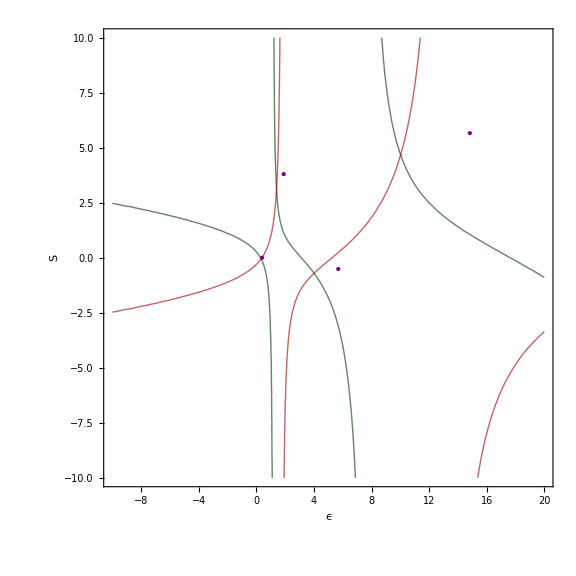

```mathematica
ContourPlot[
{FM[ϵ,S]==0,FP[ϵ,S]==0},{ϵ,-10,20},{S,-10,10},
PlotLegends->None,
FrameLabel->{Style["ϵ",Black,30],Style["S",Black,30]},
Frame->{True,True},
BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->25},
LabelStyle->Directive[25,Black,FontFamily->"Times"],
ContourStyle->{{Thick,Darker[Green,0.8],Opacity[0.6]},{Thick,Darker[Red,0.4],Opacity[0.6]}},
Epilog->{Purple,PointSize@Large,Point[{1.9,3.8}],Purple,PointSize@Large,Point[{0.4,0}],Purple,PointSize@Large,Point[{14.83,5.66}],Purple,PointSize@Large,Point[{5.69,-0.51}],Purple,PointSize@Large,Point[{34.6,-1.55}]},
Background->White,
ImageSize->Large
]
```

```mathematica
rm=-5;
rM=20;
pm=-10;
pM=10;
```

```mathematica
contourPotentialPlot1=ContourPlot[{FM[ϵ,S]==0,FP[ϵ,S]==0},{ϵ,rm,rM},{S,pm,pM},PlotRange->Full,Contours->15,Axes->False,PlotPoints->50,PlotRangePadding->0,Frame->False,ColorFunction->"DarkRainbow"];
```

```mathematica
level=-1.5
```

-1.5

```mathematica
potential1=Plot3D[{FM[ϵ,S],FP[ϵ,S],0},{ϵ,rm,rM},{S,pm,pM},PlotRange->{-1/4,1},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.8],Orange},{Opacity[.01],Cyan}},Lighting->"Neutral"];
```

```mathematica
Plot3D[{FM[ϵ,S],FP[ϵ,S],0},{ϵ,rm,rM},{S,pm,pM},PlotRange->{-500,500},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],ColorFunction->{Directive["Rainbow"],Directive["TemperatureMap"]},ImageSize->Full]
```

-Graphics3D-

```mathematica
gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{rm,pm,level},{rM,pm,level},{rM,pM,level},{rm,pM,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral",AxesStyle->Black];
```

```mathematica
Show[potential1,gr,PlotRange->All,BoxRatios->{1,1,0.6},FaceGrids->{Back,Left},Background->White,ImageSize->Large]
```

-Graphics3D-

```mathematica
plotP=ContourPlot3D[{z==αP,z==αM,z==0},{ϵ,-5,20},{S,-7,10},{z,-1,1},
AxesLabel->{"ϵ", "S"},
Background->White,
ContourStyle->{{Dashed,Blue,Opacity[0.65]},{Thick,Red,,Opacity[1.0]},{Thick,Cyan,,Opacity[0.15]}},
(*Mesh->None,*)
(*Boxed->False,*)
FaceGrids->None,
Mesh->None,
Boxed->False,
BoundaryStyle->{{1,2}->{Purple,Thick},{1,3}->{Purple,Thick},{2,3}->{Purple,Thick}}
];

pt=Point[{0.4237131621171315,-0.0336891534959879,0}];
plotPoint=Graphics3D[
{AbsolutePointSize[10],Purple,pt}
];
Show[plotP(*, plotPoint*)(*,ImageSize->Large*)(*,ViewPoint->{0,0,-Infinity}*)]
```

-Graphics3D-

## 3d Coulomb + 3d harmonic oscillator (TO DO)

#### Try to follow the same reasoning as for the quartic potential

Let us now generalize the above story to the following more generic quartic potential.
Notation: H^2=(m_1+m_2)/(m_1 m_2)hbar^2/2

GENERIC COMMENT ABOUT THIS SECTION: contrary to the case of an even potential, one here has to keep track of both the positive x and the negative x solutions

```mathematica
V[z_]:=A z +β z^2+γ/z+λ^2/z^2
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])/H^2 ψ[z];
```

Now we need to find the correct change of variable for the active variable ψ, for this, let us get inspiration from the analytical solution provided by Mathematica:

```mathematica
DSolve[eq[ψ][z]==0,ψ[z],z]//PowerExpand
```

{{ψ[z]→ⅇ^((H z (A/H^2+(z β)/H^2))/(2 √β)) z^(1/2 (1-√(1+(4 λ^2)/H^2))) C[2] HeunB[γ/H^2+(A (-1+√(1+(4 λ^2)/H^2)))/(2 H √β),A^2/(4 H^2 β)+ϵ/H^2+(√β (2-√(1+(4 λ^2)/H^2)))/H,1-√(1+(4 λ^2)/H^2),A/(H √β),(2 √β)/H,z]+ⅇ^((H z (A/H^2+(z β)/H^2))/(2 √β)) z^(√(1+(4 λ^2)/H^2)+1/2 (1-√(1+(4 λ^2)/H^2))) C[1] HeunB[γ/H^2-(A (1+1/2 (-1+√(1+(4 λ^2)/H^2))))/(H √β),A^2/(4 H^2 β)+ϵ/H^2+(√β (2+√(1+(4 λ^2)/H^2)))/H,2 (1+1/2 (-1+√(1+(4 λ^2)/H^2))),A/(H √β),(2 √β)/H,z]}}

So now we have the exponential change of variable.
Remains the (z+1)^(some power) to fix. Let us call the generic power μ

```mathematica
eq2Plus[w_]:=z↦1/(ⅇ^(A z+B z^2) z^η(z+1)^μ)eq[z↦ ⅇ^(A z+B z^2) z^η(z+1)^μ w[z]][z]
```

```mathematica
Coefficient[eq2Plus[w][z],w''[z]]//FullSimplify
Coefficient[eq2Plus[w][z],w'[z]]//Together
Coefficient[eq2Plus[w][z],w[z]]//Together
```

1

(2 (A z+A z^2+2 B z^2+2 B z^3+η+z η+z μ))/(z (1+z))

1/(H^2 z^2 (1+z)^2)(A^2 H^2 z^2+2 B H^2 z^2-A z^3+2 A^2 H^2 z^3+4 B H^2 z^3+4 A B H^2 z^3-2 A z^4+A^2 H^2 z^4+2 B H^2 z^4+8 A B H^2 z^4+4 B^2 H^2 z^4-A z^5+4 A B H^2 z^5+8 B^2 H^2 z^5+4 B^2 H^2 z^6-z^4 β-2 z^5 β-z^6 β-z γ-2 z^2 γ-z^3 γ+z^2 ϵ+2 z^3 ϵ+z^4 ϵ-H^2 η-2 H^2 z η+2 A H^2 z η-H^2 z^2 η+4 A H^2 z^2 η+4 B H^2 z^2 η+2 A H^2 z^3 η+8 B H^2 z^3 η+4 B H^2 z^4 η+H^2 η^2+2 H^2 z η^2+H^2 z^2 η^2-λ^2-2 z λ^2-z^2 λ^2-H^2 z^2 μ+2 A H^2 z^2 μ+2 A H^2 z^3 μ+4 B H^2 z^3 μ+4 B H^2 z^4 μ+2 H^2 z η μ+2 H^2 z^2 η μ+H^2 z^2 μ^2)

```mathematica
PolynomialRemainder[(A^2 H^2 z^2+2 B H^2 z^2-A z^3+2 A^2 H^2 z^3+4 B H^2 z^3+4 A B H^2 z^3-2 A z^4+A^2 H^2 z^4+2 B H^2 z^4+8 A B H^2 z^4+4 B^2 H^2 z^4-A z^5+4 A B H^2 z^5+8 B^2 H^2 z^5+4 B^2 H^2 z^6-z^4 β-2 z^5 β-z^6 β-z γ-2 z^2 γ-z^3 γ+z^2 ϵ+2 z^3 ϵ+z^4 ϵ-H^2 η-2 H^2 z η+2 A H^2 z η-H^2 z^2 η+4 A H^2 z^2 η+4 B H^2 z^2 η+2 A H^2 z^3 η+8 B H^2 z^3 η+4 B H^2 z^4 η+H^2 η^2+2 H^2 z η^2+H^2 z^2 η^2-λ^2-2 z λ^2-z^2 λ^2-H^2 z^2 μ+2 A H^2 z^2 μ+2 A H^2 z^3 μ+4 B H^2 z^3 μ+4 B H^2 z^4 μ+2 H^2 z η μ+2 H^2 z^2 η μ+H^2 z^2 μ^2),z^2 (1+z)^2,z]
```

-H^2 η+H^2 η^2-λ^2+z^3 (-γ+2 A H^2 η+2 A H^2 μ-4 B H^2 μ)+z (-γ-2 H^2 η+2 A H^2 η+2 H^2 η^2-2 λ^2+2 H^2 η μ)+z^2 (-2 γ-H^2 η+4 A H^2 η+H^2 η^2-λ^2-H^2 μ+2 A H^2 μ-4 B H^2 μ+2 H^2 η μ+H^2 μ^2)

```mathematica
PolynomialRemainder[(A z+A z^2+2 B z^2+2 B z^3+η+z η+z μ),z(1+z),z]
```

η+z (η+μ)

We perform a change of passive variable to move to the [0,1] segment

```mathematica
Solve[{x==z/(z+1)},{z}]//FullSimplify
Solve[{x==-z/(-z+1)},{z}]//FullSimplify
```

{{z→-x/(-1+x)}}

{{z→x/(-1+x)}}

```mathematica
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
```

Now we need to fix the power μ in order for the coefficient of w[x] to be a polynomial in x

```mathematica
Coefficient[eq3Plus[w][x],w[x]]//FullSimplify
Coefficient[eq3Plus[w][x],w'[x]]//FullSimplify
Coefficient[eq3Plus[w][x],w''[x]]//FullSimplify
```

1/(8 H^2 β λ^4)(2 λ^2 ((-1+x)^2 β γ^2+A^2 x^2 λ^2+4 β (-A x+(-1+x) γ+ϵ) λ^2)+(H-H x)^2 β γ (γ+2 λ^2) (1+√(1+(4 λ^2)/H^2))-2 H √β λ^2 (4 β λ^2 (-2+√(1+(4 λ^2)/H^2))+2 x β γ (1+√(1+(4 λ^2)/H^2))-A (-1+x) (2 λ^2 (-2+√(1+(4 λ^2)/H^2))+x (γ+2 λ^2+γ √(1+(4 λ^2)/H^2)))))

((-1+x) (2 x^2 (A (-1+x)-2 β) λ^2+H (-1+x)^2 √β (2 λ^2 (-1+√(1+(4 λ^2)/H^2))+x (γ+4 λ^2+γ √(1+(4 λ^2)/H^2)))))/(2 H x √β λ^2)

(-1+x)^4

μ should be such that -1+x divides the above numerator

```mathematica
muPlus=Solve[PolynomialRemainder[(A^2 x+2 A H (-1+x) √β (-1+√(1+(4 λ^2)/H^2)-2 x μ)+4 β ((-1+x) γ+x ϵ-H^2 (-1+x)^2 μ (-1+x+√(1+(4 λ^2)/H^2)-x μ)+H x √β (2-√(1+(4 λ^2)/H^2)+2 x μ))),x,x]==0,μ][[1,1,2]]//FullSimplify
```

-A/(2 H √β)-(γ (1+√(1+(4 λ^2)/H^2)))/(4 λ^2)

That is a great success. So now we can perform the change of variable explicitly.

```mathematica
V[z_]:=A z +β z^2+γ/z+λ^2/z^2
eq[ψ_]:=z↦ψ''[z]+(ϵ-V[z])/H^2 ψ[z];
eq2Plus[w_]:=z↦1/(ⅇ^((H z (A/H^2+(z β)/H^2))/(2 √β)) z^(1/2 (1-√(1+(4 λ^2)/H^2)))(z+1)^(-A/(2 H √β)-(γ (1+√(1+(4 λ^2)/H^2)))/(4 λ^2)))eq[z↦ ⅇ^((H z (A/H^2+(z β)/H^2))/(2 √β)) z^(1/2 (1-√(1+(4 λ^2)/H^2)))(z+1)^(-A/(2 H √β)-(γ (1+√(1+(4 λ^2)/H^2)))/(4 λ^2))w[z]][z]
eq3Plus[w_]:=x↦(eq2Plus[w][z]/.w->(w[#1/(#1+1)]&)/.z->x/(1-x))//FullSimplify
```

The coefficients of the ODE are simple polynomials now. Let us extract and name the coefficients of those polynomials

```mathematica
CoefficientList[Coefficient[eq3Plus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Plus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

CoefficientList::poly: (-4 H^2 x β γ λ^2+12 H^2 x^2 β γ λ^2-12 H^2 x^3 β γ λ^2+4 H^2 x^4 β γ λ^2+8 A H x^2 √β λ^4-16 A H «1» √β λ^4+8 A H x^4 √β λ^4+8 H^2 β λ^4-40 H^2 x β λ^4+72 H^2 x^2 β λ^4+«12»)/(8 H^2 x β λ^4) is not a polynomial.

{-5+3 √(1+(4 λ^2)/H^2)+(1-√(1+(4 λ^2)/H^2))/x-(γ (1+√(1+(4 λ^2)/H^2)))/(2 λ^2),9+(A+2 β)/(H √β)-3 √(1+(4 λ^2)/H^2)+(3 γ (1+√(1+(4 λ^2)/H^2)))/(2 λ^2),-7-(2 (A+β))/(H √β)+√(1+(4 λ^2)/H^2)-(3 γ (1+√(1+(4 λ^2)/H^2)))/(2 λ^2),A/(H √β)+(γ+4 λ^2+γ √(1+(4 λ^2)/H^2))/(2 λ^2)}

{(-γ+ϵ)/H^2+γ^2/(4 H^2 λ^2)-((A+2 β) (-2+√(1+(4 λ^2)/H^2)))/(2 H √β)+(γ (γ+2 λ^2) (1+√(1+(4 λ^2)/H^2)))/(8 λ^4),(-2 A+γ (2-γ/λ^2))/(2 H^2)-(γ (γ+2 λ^2) (1+√(1+(4 λ^2)/H^2)))/(4 λ^4)-(-2 A λ^2 (-3+√(1+(4 λ^2)/H^2))+A γ (1+√(1+(4 λ^2)/H^2))+2 β γ (1+√(1+(4 λ^2)/H^2)))/(4 H √β λ^2),(2 λ^2 (β γ^2+A^2 λ^2)+H^2 β γ (γ+2 λ^2) (1+√(1+(4 λ^2)/H^2))+2 A H √β λ^2 (γ+2 λ^2+γ √(1+(4 λ^2)/H^2)))/(8 H^2 β λ^4)}

```mathematica
a=1;
b=-4;
c=6;
d=-4;
e=1;
f=-(γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+32 H λ^5)/(8 H λ^5);
g=(3 γ^3-4 γ (3 β+γ) λ^2+8 (3 A+2 β-γ) λ^4+96 H λ^5)/(8 H λ^5);
h=-(3 γ^3-2 γ (6 β+γ) λ^2+8 (3 A+β-γ) λ^4+96 H λ^5+16 λ^6)/(8 H λ^5);
i=(γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ))/(8 H λ^5);
j=1/(256 H^2 λ^10)(γ^6-4 γ^4 (2 β+γ) λ^2+4 γ^2 (4 β^2+8 β γ+γ (4 A+γ)) λ^4+48 H γ^3 λ^5-32 (A+β) γ (2 β+γ) λ^6-64 H γ (3 β+γ) λ^7+64 (A+β)^2 λ^8+128 H (3 A+2 β-γ) λ^9+256 (2 H^2+ϵ) λ^10);
k=-((γ^3-2 γ (2 β+γ) λ^2+8 (A+β-γ) λ^4+32 H λ^5+16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ)))/(128 H^2 λ^10);l=((γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A+4 H λ)))/(256 H^2 λ^10);
```

```mathematica
CoefficientList[Coefficient[eq3Minus[w][x],w''[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w'[x]],x]//FullSimplify
CoefficientList[Coefficient[eq3Minus[w][x],w[x]],x]//FullSimplify
```

{1,-4,6,-4,1}

{(γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-32 H λ^5)/(8 H λ^5),(-3 γ^3-4 γ (-3 β+γ) λ^2+8 (-3 A+2 β+γ) λ^4+96 H λ^5)/(8 H λ^5),(3 γ^3+2 γ (-6 β+γ) λ^2-8 (-3 A+β+γ) λ^4-96 H λ^5-16 λ^6)/(8 H λ^5),-(γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ))/(8 H λ^5)}

{1/(256 H^2 λ^10)(γ^6+4 γ^4 (-2 β+γ) λ^2+4 γ^2 (4 β^2-8 β γ+γ (4 A+γ)) λ^4-48 H γ^3 λ^5-32 (-A+β) γ (-2 β+γ) λ^6-64 H γ (-3 β+γ) λ^7+64 (A-β)^2 λ^8+128 H (-3 A+2 β+γ) λ^9+256 (2 H^2+ϵ) λ^10),-((γ^3+2 γ (-2 β+γ) λ^2-8 (-A+β+γ) λ^4-32 H λ^5-16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(128 H^2 λ^10),((γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(256 H^2 λ^10)}

```mathematica
aa=1;
bb=-4;
cc=6;
dd=-4;
ee=1;
ff=(γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-32 H λ^5)/(8 H λ^5);
gg=(-3 γ^3-4 γ (-3 β+γ) λ^2+8 (-3 A+2 β+γ) λ^4+96 H λ^5)/(8 H λ^5);
hh=(3 γ^3+2 γ (-6 β+γ) λ^2-8 (-3 A+β+γ) λ^4-96 H λ^5-16 λ^6)/(8 H λ^5);
ii=-(γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ))/(8 H λ^5);
jj=1/(256 H^2 λ^10)(γ^6+4 γ^4 (-2 β+γ) λ^2+4 γ^2 (4 β^2-8 β γ+γ (4 A+γ)) λ^4-48 H γ^3 λ^5-32 (-A+β) γ (-2 β+γ) λ^6-64 H γ (-3 β+γ) λ^7+64 (A-β)^2 λ^8+128 H (-3 A+2 β+γ) λ^9+256 (2 H^2+ϵ) λ^10);
kk=-((γ^3+2 γ (-2 β+γ) λ^2-8 (-A+β+γ) λ^4-32 H λ^5-16 λ^6) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(128 H^2 λ^10);ll=((γ^3-4 β γ λ^2+8 λ^4 (A-4 H λ)) (γ^3-4 β γ λ^2+8 λ^4 (A-2 H λ)))/(256 H^2 λ^10);
```

Ansatz for w(x)=∑α_n x^n, we get the following difference equations, exactly the same as in the previous section because it is for generic coefficients abcdefghijkl

```mathematica
diffEqPlus[n_]:=(n+1)(n+2)a Subscript[α, n+2]+(n(n+1)b+(n+1)f)Subscript[α, n+1]+((n-1)n c+n g+j)Subscript[α, n]+((n-2)(n-1)d+(n-1)h+k)Subscript[α, n-1]+((n-3)(n-2)e+(n-2)i+l)Subscript[α, n-2]
diffEqMinus[n_]:=(n+1)(n+2)aa Subscript[δ, n+2]+(n(n+1)bb+(n+1)ff)Subscript[δ, n+1]+((n-1)n cc+n gg+jj)Subscript[δ, n]+((n-2)(n-1)dd+(n-1)hh+kk)Subscript[δ, n-1]+((n-3)(n-2)ee+(n-2)ii+ll)Subscript[δ, n-2]
```

Now we need to generalize the choice of initial conditions C0 and C1 in order to be able to extract the even level energy spectrum, and in particular the ground state energy.
Let us recall that for the previous potential (γ->0, β->1), we had C0=1 and C1=1+1/(2λ).

```mathematica
psiPlus[z_]:=Exp[-(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)](z+1)^(-(γ^3-4 β γ λ^2+8 λ^4 (A+2 H λ))/(16 H λ^5))(Subscript[α, 0]+Subscript[α, 1] z/(z+1)+Subscript[α, 2](z/(z+1))^2)
psiMinus[z_]:=Exp[(z (-3 γ^2+6 (2 β+z γ) λ^2+8 z^2 λ^4))/(24 H λ^3)](-z+1)^(-(-γ^3+4 β γ λ^2+8 λ^4 (-A+2 H λ))/(16 H λ^5))(Subscript[δ, 0]+Subscript[δ, 1]-z/(-z+1)+Subscript[δ, 2](-z/(-z+1))^2)
```

```mathematica
psiPlus'[0]/.rule//FullSimplify
psiMinus'[0]/.rule//FullSimplify
```

-((1+A+2 λ) α_0)/(2 λ)+α_1

((1-A+2 λ) δ_0)/(2 λ)-δ_1

```mathematica
psiPlus'[0]//FullSimplify
psiMinus'[0]//FullSimplify
```

-((γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+16 H λ^5) α_0)/(16 H λ^5)+α_1

-((γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-16 H λ^5) δ_0)/(16 H λ^5)-δ_1

```mathematica
C0=1;
C1=S+((γ^3-2 γ (2 β+γ) λ^2+8 (A+β) λ^4+16 H λ^5) Subscript[α, 0])/(16 H λ^5)C0;
CC0=1;
CC1=-S-((γ^3+2 γ (-2 β+γ) λ^2+8 (A-β) λ^4-16 H λ^5) Subscript[δ, 0])/(16 H λ^5)CC0;
initialEqPlus={Subscript[α, 0]-C0,Subscript[α, 1]-C1,2a Subscript[α, 2]+f Subscript[α, 1]+j Subscript[α, 0],6a Subscript[α, 3]+2(b+f)Subscript[α, 2]+(g+j)Subscript[α, 1]+k Subscript[α, 0]};
initialEqMinus={Subscript[δ, 0]-CC0,Subscript[δ, 1]-CC1,2aa Subscript[δ, 2]+ff Subscript[δ, 1]+jj Subscript[δ, 0],6aa Subscript[δ, 3]+2(bb+ff)Subscript[δ, 2]+(gg+jj)Subscript[δ, 1]+kk Subscript[δ, 0]};
```

We solve for the coefficients of the series expansion for a large value of n

```mathematica
Nmax=20;
αlargePlus=Solve[Thread[Join[initialEqPlus,Table[diffEqPlus[n],{n,2,Nmax-2}]]==0],Table[Subscript[α, m],{m,0,Nmax}]][[1,Nmax+1,2]];
αlargeMinus=Solve[Thread[Join[initialEqMinus,Table[diffEqMinus[n],{n,2,Nmax-2}]]==0],Table[Subscript[δ, m],{m,0,Nmax}]][[1,Nmax+1,2]];
```

Check that we recover the result for the simpler potential

```mathematica
FindRoot[{αlargePlus,αlargeMinus}/.{λ->1,A->1.0,γ->0,H->1,β->1},{{ϵ,1},{S,-10}}]
```

{ϵ→1.29921,S→-0.318716}

The new result

```mathematica
FindRoot[{αlargePlus,αlargeMinus}/.{λ->1,A->1.0,γ->1,H->1,β->1},{{ϵ,1},{S,-10}}]
```

{ϵ→1.03413,S→-0.535406}

## Anharmonic oscillator

### Discretization (toy model)

```mathematica
V[x_]=(-x^2/2+x^4/24)20;
```

```mathematica
PlotV=Plot[V[x],{x,-3.5,3.5}];
```

```mathematica
n=300;
L=10;
δx=L/n;
```

```mathematica
M=SparseArray[{{i_,i_}->V[-L/2+(i-1)δx]+1/δx^2,{i_,j_}/;Abs[j-i]==1->-1/(2 δx^2)},{n+1,n+1}]
```

SparseArray[…]

```mathematica
Normal@M
```

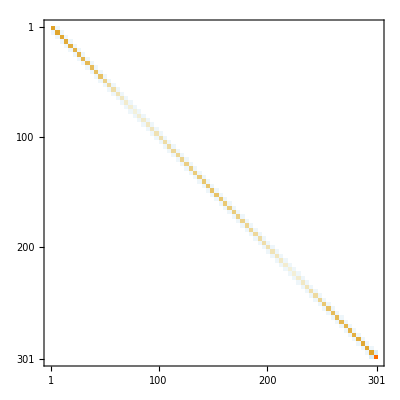

```mathematica
MatrixPlot@M
```

```mathematica
?Table
```

```mathematica
M=N@M;
```

```mathematica
Normal@M[[1;;10,1;;10]]//MatrixForm
```

(1170.83 | -450. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-450. | 1160.4 | -450. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -450. | 1150.23 | -450. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -450. | 1140.3 | -450. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -450. | 1130.62 | -450. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -450. | 1121.17 | -450. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -450. | 1111.97 | -450. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -450. | 1103. | -450. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -450. | 1094.25 | -450.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -450. | 1085.74)

```mathematica
Eigensystem@M
```

Eigensystem::arh: Because finding 301 out of the 301 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{{1998.76,1998.76,1943.3,1943.3,1902.16,1902.16,1869.14,1869.14,1841.85,1841.85,1819.09,1819.09,277,14.7174,11.8488,-9.72143,-9.72,9.11562,6.54994,-4.85438,-4.80738,4.10833,2.14064,-0.995742,-0.353902},{1}}
 |  |  |  |

```mathematica
Eigensystem@M//Quiet
```

{{1998.76,1998.76,1943.3,1943.3,1902.16,1902.16,1869.14,1869.14,1841.85,1841.85,1819.09,1819.09,277,14.7174,11.8488,-9.72143,-9.72,9.11562,6.54994,-4.85438,-4.80738,4.10833,2.14064,-0.995742,-0.353902},{1}}
 |  |  |  |

```mathematica
Eigensystem@N@{{1,2,3},{2,3,4},{5,7,7}}
```

{{12.3127,-1.17435,-0.138319},{{-0.301689,-0.430234,-0.850813},{-0.618351,-0.368764,0.694013},{0.684109,-0.699469,0.206734}}}

Eigensystem::arh: Because finding 301 out of the 301 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

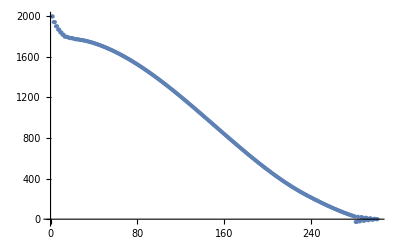

```mathematica
Eigensystem[M][[1]]//ListPlot
```

```mathematica
Eigensystem@N@{{1,2,3},{2,3,4},{5,7,7}}//MatrixForm
```

(12.3127 | -1.17435 | -0.138319
{-0.301689,-0.430234,-0.850813} | {-0.618351,-0.368764,0.694013} | {0.684109,-0.699469,0.206734})

```mathematica
Eigensystem@N@{{1,2,3},{2,3,4},{5,7,7}}//Transpose//Sort//Transpose//MatrixForm
```

(-1.17435 | -0.138319 | 12.3127
{-0.618351,-0.368764,0.694013} | {0.684109,-0.699469,0.206734} | {-0.301689,-0.430234,-0.850813})

```mathematica
es=Eigensystem[M]//Transpose//Sort//#[[1;;10]]&//Transpose//Quiet;
```

```mathematica
es[[1]]
```

{-26.882,-26.882,-20.8314,-20.8314,-15.091,-15.091,-9.72143,-9.72,-4.85438,-4.80738}

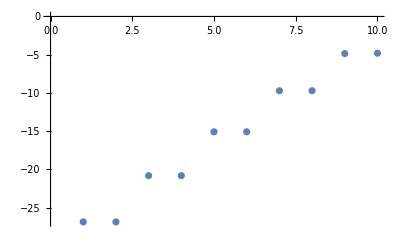

```mathematica
es[[1]]//ListPlot
```

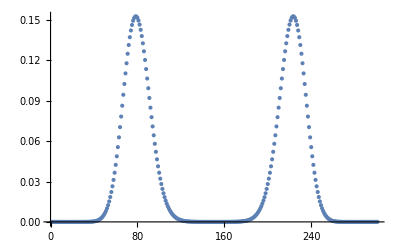

```mathematica
es[[2,1]]//ListPlot
```

```mathematica
es[[2,4]]//Norm
```

1.

```mathematica
PlotWF=Table[ {Range[-L/2,L/2,δx],es[[1,j]]+1/(√δx)es[[2,j]]}ᵀ,{j,1,10}]//ListPlot[#,Joined->True]&;
```

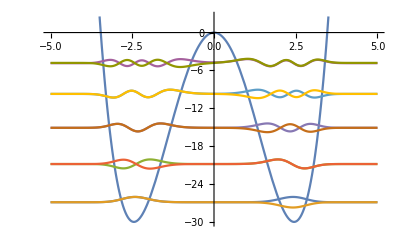

```mathematica
Show[PlotV,PlotWF,PlotRange->All]
```

### Discretization (our model)

```mathematica
latexCouplings={A->α,λ->√δ};
physicalCouplings={α->-(m1 q2+m2 q1)/(m1+m2)τ,β->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 ω2^2+m2 ω1^2)/(m1+m2),γ->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,δ->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
HHrule={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,ω1->0.4273,ω2->0.4273,HBAR->1};
paramRules={r->1,τ->0};
```

```mathematica
v[x_]=A x +β x^2+γ x^3+λ^2 x^4;
V[x_]:=(v[x]//.latexCouplings//.physicalCouplings//.HHrule//.paramRules)
```

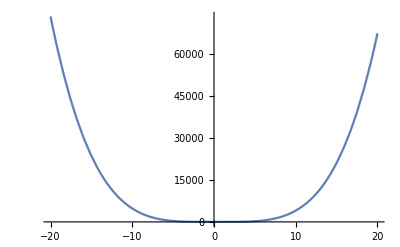

```mathematica
PlotV=Plot[V[x],{x,-20,20}]
```

```mathematica
n=2000;
L=50;
δx=L/n;
```

```mathematica
M=SparseArray[{{i_,i_}->V[-L/2+(i-1)δx]+(HBAR^2/((m1 m2)/(m1+m2))//.HHrule)1/δx^2,{i_,j_}/;Abs[j-i]==1->-1/(2 δx^2)(HBAR^2/((m1 m2)/(m1+m2))//.HHrule)},{n+1,n+1}]
```

SparseArray[…]

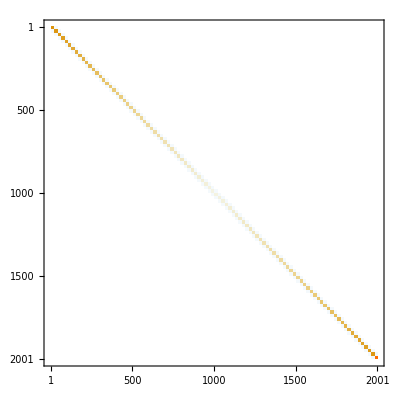

```mathematica
MatrixPlot@M
```

```mathematica
?Table
```

```mathematica
M=N@M;
```

```mathematica
Normal@M[[1;;10,1;;10]]//MatrixForm
```

(182625. | -2623.38 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2623.38 | 181923. | -2623.38 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -2623.38 | 181223. | -2623.38 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -2623.38 | 180525. | -2623.38 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -2623.38 | 179829. | -2623.38 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -2623.38 | 179135. | -2623.38 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2623.38 | 178443. | -2623.38 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -2623.38 | 177753. | -2623.38 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -2623.38 | 177066. | -2623.38
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2623.38 | 176380.)

```mathematica
Eigensystem@M//Quiet
```

{{186070.,184264.,182835.,181612.,180531.,179560.,178679.,177873.,177127.,1983,40.7297,34.5298,28.5943,22.9501,17.632,12.6875,8.18703,4.24099,1.21559},{1}}
 |  |  |  |

Eigensystem::arh: Because finding 2001 out of the 2001 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

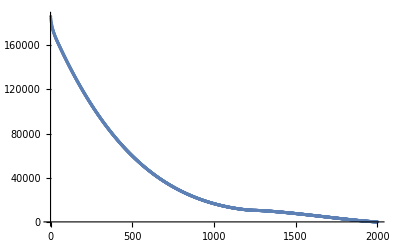

```mathematica
Eigensystem[M][[1]]//ListPlot
```

```mathematica
es=Eigensystem[M]//Transpose//Sort//#[[1;;10]]&//Transpose//Quiet;
```

```mathematica
es[[1]]
```

{1.21559,4.24099,8.18703,12.6875,17.632,22.9501,28.5943,34.5298,40.7297,47.1726}

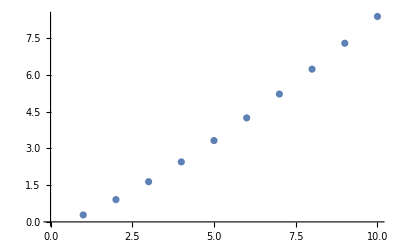

```mathematica
es[[1]]//ListPlot
```

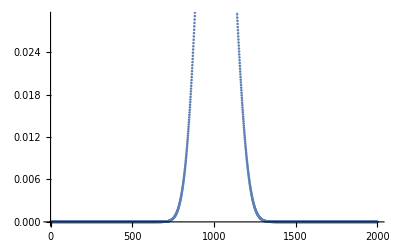

```mathematica
es[[2,1]]//ListPlot
```

```mathematica
es[[2,4]]//Norm
```

1.

```mathematica
PlotWF=Table[ {Range[-L/2,L/2,δx],es[[1,j]]+1/(√δx)es[[2,j]]}ᵀ,{j,1,10}]//ListPlot[#,Joined->True]&;
```

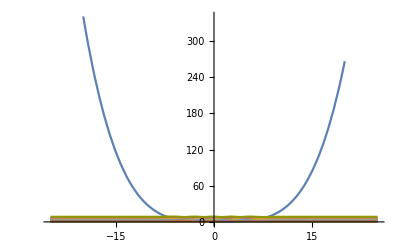

```mathematica
Show[PlotV,PlotWF,PlotRange->Automatic]
```

### Rayleigh-Ritz Method (toy model)

```mathematica
SuperDagger[a]//FullForm
```

SuperDagger[a]

```mathematica
a·b//FullForm
```

CenterDot[a,b]

```mathematica
?CenterDot
```

```mathematica
?CircleTimes
```

```mathematica
a⊗b//FullForm
```

CircleTimes[a,b]

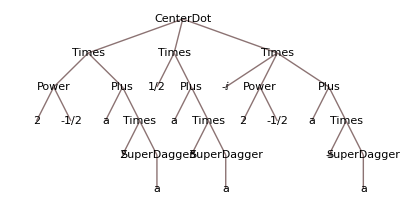

```mathematica
(a+2 SuperDagger[a])/(√2)·(a+3 SuperDagger[a])/(√4)·(a-I SuperDagger[a])/(√2 I)//TreeForm
```

```mathematica
(a+2 SuperDagger[a])/(√2)·(a+3 SuperDagger[a])/(√4)·(a-I SuperDagger[a])/(√2 I)//Expand
```

(a+2 a^†)/(√2)·(1/2 (a+3 a^†))·-(ⅈ (a-ⅈ a^†))/(√2)

```mathematica
ClearAll[n]
```

```mathematica
Ket[n]
```

n

```mathematica
SuperDagger[a]·n
```

```mathematica
ℙ=(SuperDagger[a]-a)/(√2 I);
𝕏=(SuperDagger[a]+a)/(√2);
```

```mathematica
rules={
a___·(b_+c_)·d___->a·b·d+a·c·d,
a___·(b_ c_)·d___/;NumericQ[b]->b(a·c·d),
b___·a·n_->√(n-1)b·n-1,
b___·SuperDagger[a]·n_->√n b·n+1,
CenterDot[a_]->a
};
(* Note that 1 is the vacuum in these conventions *)
```

```mathematica
(*
rules={
before___·(number_ operator_)·after___/;NumericQ[number]->number(before·operator·after),
before___·(op1_+op2_)·after___->before·op1·after+before·op2·after,
before___·a·a^†·after___->before·a^†·a·after+before·after,
CenterDot[a_]->a
};
*)
```

```mathematica
1/2 ℙ·ℙ·n+1/2 𝕏·𝕏·n//.rules//Simplify
```

1/2 (-1+2 n) n

```mathematica
1/2 ℙ·ℙ·n-20 1/2 𝕏·𝕏·n+20 1/24 𝕏·𝕏·𝕏·𝕏·n//.rules//Simplify
```

1/24 (5 √(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+4 √(-2+n) √(-1+n) (-39+5 n) -2+n+129 n-258 n n+30 n^2 n-116 √n √(1+n) 2+n+20 n^(3/2) √(1+n) 2+n+5 √n √(1+n) √(2+n) √(3+n) 4+n)

```mathematica
HonKet=1/2 ℙ·ℙ·n-20 1/2 𝕏·𝕏·n+20 1/24 𝕏·𝕏·𝕏·𝕏·n//.rules//Collect[#,Ket[_], Simplify]&
```

5/24 √(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+1/6 √(-2+n) √(-1+n) (-39+5 n) -2+n+1/8 (43-86 n+10 n^2) n+1/6 √n √(1+n) (-29+5 n) 2+n+5/24 √n √(1+n) √(2+n) √(3+n) 4+n

```mathematica
M=100;
```

```mathematica
options=Cases[HonKet,Ket[a_]->a,∞]
```

{-4+n,-2+n,n,2+n,4+n}

```mathematica
matrixRules=Table[{n_,m_}/;m==aa->Coefficient[HonKet,Ket[a]]/.aa->a,{a,options}]
```

{{n_,m_}/;m==-4+n→5/24 √(-4+n) √(-3+n) √(-2+n) √(-1+n),{n_,m_}/;m==-2+n→1/6 √(-2+n) √(-1+n) (-39+5 n),{n_,m_}/;m==n→1/8 (43-86 n+10 n^2),{n_,m_}/;m==2+n→1/6 √n √(1+n) (-29+5 n),{n_,m_}/;m==4+n→5/24 √n √(1+n) √(2+n) √(3+n)}

```mathematica
Hmatrix=N[#,30]&@SparseArray[matrixRules,{M,M}]
```

SparseArray[…]

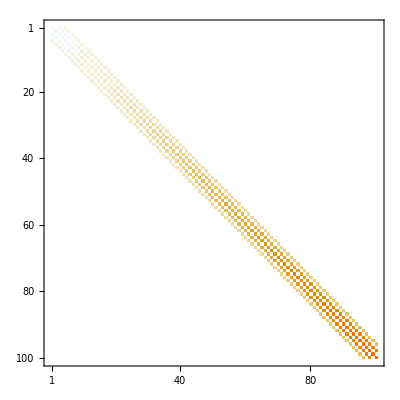

```mathematica
MatrixPlot@Hmatrix
```

```mathematica
Hmatrix//Eigenvalues//Sort//Take[#,10]&//TableForm
```

-26.8807132200142652677619488657
-26.8807132191845513006086447811
-20.8251911255743773895414139612
-20.8251909038628526092441633164
-15.0763261586985867047363328696
-15.0763017649924014706645760807
-9.69628747141710055513701644189
-9.6948339001932005935024576717
-4.82019464189221199332402881491
-4.77196449065986379538014683566

### Rayleigh-Ritz Method (our model)

```mathematica
latexCouplings={A->α,λ->√δ};
physicalCouplings={α->-(m1 q2+m2 q1)/(m1+m2)τ,β->(m1 m2)/(m1+m2)^2(2 q1 q2)/r^3+1/2(m1 m2)/(m1+m2)(m1 ω2^2+m2 ω1^2)/(m1+m2),γ->-(m1 m2)/(m1+m2)^2(3 q1 q2)/r^4,δ->(2m1 m2(2 m1^2+3m1 m2+2 m2^2))/(m1+m2)^4(q1 q2)/r^5,H->√((m1+m2)/(m1 m2)HBAR^2/2)};
HHrule={m1->0.6099,m2->0.6099,q1->0.7080,q2->0.7080,ω1->0.4273,ω2->0.4273,HBAR->1};
paramRules={r->1,τ->0};
```

```mathematica
v[x_]=A x +β x^2+γ x^3+λ^2 x^4;
V[x_]:=(v[x]//.latexCouplings//.physicalCouplings//.HHrule//.paramRules)
```

```mathematica
V[x_]=
```

```mathematica
ℙ=(SuperDagger[a]-a)/(√2 I);
𝕏=(SuperDagger[a]+a)/(√2);
```

```mathematica
rules={
a___·(b_+c_)·d___->a·b·d+a·c·d,
a___·(b_ c_)·d___/;NumericQ[b]->b(a·c·d),
b___·a·n_->√(n-1)b·n-1,
b___·SuperDagger[a]·n_->√n b·n+1,
CenterDot[a_]->a
};
(* Note that 1 is the vacuum in these conventions *)
```

```mathematica
(*
rules={
before___·(number_ operator_)·after___/;NumericQ[number]->number(before·operator·after),
before___·(op1_+op2_)·after___->before·op1·after+before·op2·after,
before___·a·a^†·after___->before·a^†·a·after+before·after,
CenterDot[a_]->a
};
*)
```

```mathematica
1/2 ℙ·ℙ·n+1/2 𝕏·𝕏·n//.rules//Simplify
```

1/2 (-1+2 n) n

```mathematica
1/2 ℙ·ℙ·n-20 1/2 𝕏·𝕏·n+20 1/24 𝕏·𝕏·𝕏·𝕏·n//.rules//Simplify
```

1/24 (5 √(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+4 √(-2+n) √(-1+n) (-39+5 n) -2+n+129 n-258 n n+30 n^2 n-116 √n √(1+n) 2+n+20 n^(3/2) √(1+n) 2+n+5 √n √(1+n) √(2+n) √(3+n) 4+n)

```mathematica
HonKet=1/2 ℙ·ℙ·n-20 1/2 𝕏·𝕏·n+20 1/24 𝕏·𝕏·𝕏·𝕏·n//.rules//Collect[#,Ket[_], Simplify]&
```

5/24 √(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+1/6 √(-2+n) √(-1+n) (-39+5 n) -2+n+1/8 (43-86 n+10 n^2) n+1/6 √n √(1+n) (-29+5 n) 2+n+5/24 √n √(1+n) √(2+n) √(3+n) 4+n

```mathematica
M=100;
```

```mathematica
options=Cases[HonKet,Ket[a_]->a,∞]
```

{-4+n,-2+n,n,2+n,4+n}

```mathematica
matrixRules=Table[{n_,m_}/;m==aa->Coefficient[HonKet,Ket[a]]/.aa->a,{a,options}]
```

{{n_,m_}/;m==-4+n→5/24 √(-4+n) √(-3+n) √(-2+n) √(-1+n),{n_,m_}/;m==-2+n→1/6 √(-2+n) √(-1+n) (-39+5 n),{n_,m_}/;m==n→1/8 (43-86 n+10 n^2),{n_,m_}/;m==2+n→1/6 √n √(1+n) (-29+5 n),{n_,m_}/;m==4+n→5/24 √n √(1+n) √(2+n) √(3+n)}

```mathematica
Hmatrix=N[#,30]&@SparseArray[matrixRules,{M,M}]
```

SparseArray[…]

```mathematica
MatrixPlot@Hmatrix
```

-Graphics-

```mathematica
Hmatrix//Eigenvalues//Sort//Take[#,10]&//TableForm
```

-26.8807132200142652677619488657
-26.8807132191845513006086447811
-20.8251911255743773895414139612
-20.8251909038628526092441633164
-15.0763261586985867047363328696
-15.0763017649924014706645760807
-9.69628747141710055513701644189
-9.6948339001932005935024576717
-4.82019464189221199332402881491
-4.77196449065986379538014683566

## Playground

```mathematica
Solve[Thread[CoefficientList[α(x+β)^2+γ(x+δ)^4-(a x+b x^2+c x^3+d x^4),x]==0],{α,β,γ,δ}]//Simplify
```

{}

```mathematica
CoefficientList[α(x+β)^2+γ(x+δ)^4-(a x+b x^2+c x^3+d x^4),x]
```

{α β^2+γ δ^4,-a+2 α β+4 γ δ^3,-b+α+6 γ δ^2,-c+4 γ δ,-d+γ}